```mathematica
(*1*)
f1[t_]:=Cos[ω0 t];
f2[t_]:=UnitBox[t/5];
f3[t_]:=Piecewise[{{Exp[2 t],t<0},{Exp[-3t],t>=0}}];
FourierTransform[f1[t],t,ω]
FourierTransform[f2[t],t,ω]
FourierTransform[f3[t],t,ω]
```

√(π/2) DiracDelta[ω-ω0]+√(π/2) DiracDelta[ω+ω0]

(5 Sinc[(5 ω)/2])/(√(2 π))

5/(√(2 π) (6+ⅈ ω+ω^2))

```mathematica
F1[ω_]:=1/(1+ω^2);
F2[ω_]:=2 Sin[3 (ω-2 Pi)]/(ω-2 Pi);
F3[ω_]:=Cos[4 ω+Pi/3];
InverseFourierTransform[F1[t],t,ω]
InverseFourierTransform[F2[t],t,ω]
InverseFourierTransform[F3[t],t,ω]
```

ⅇ^(-Abs[ω]) √(π/2)

√(π/2) (Sign[3-ω]+Sign[3+ω]) (Cos[2 π ω]-ⅈ Sin[2 π ω])

1/2 √(π/2) DiracDelta[-4+ω]+1/2 ⅈ √((3 π)/2) DiracDelta[-4+ω]+1/2 √(π/2) DiracDelta[4+ω]-1/2 ⅈ √((3 π)/2) DiracDelta[4+ω]

```mathematica
(*2*)
Clear["`*"];
f11[t_]:=Exp[-2 t]UnitStep[t];
f12[t_]:=Exp[-2 (t-3)]UnitStep[t-3];
f21[t_]:=Exp[-3 Abs[t]] UnitStep[t];
f22[t_]:=2 Exp[-3 t] UnitStep[t]+2 Exp[3 t] UnitStep[-t];
F11=FourierTransform[f11[t],t,ω]
F12=FourierTransform[f12[t],t,ω]
F21=FourierTransform[f21[t],t,ω]
F22=FourierTransform[f22[t],t,ω]
```

ⅈ/(√(2 π) (2 ⅈ+ω))

(ⅈ ⅇ^(3 ⅈ ω))/(√(2 π) (2 ⅈ+ω))

ⅈ/(√(2 π) (3 ⅈ+ω))

(6 √(2/π))/(9+ω^2)

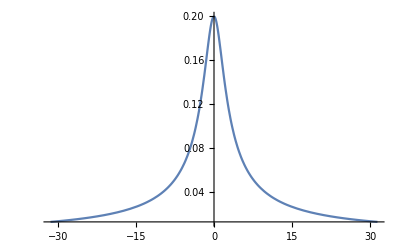

-Graphics-

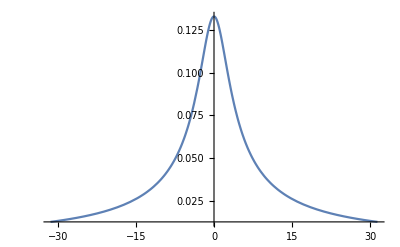

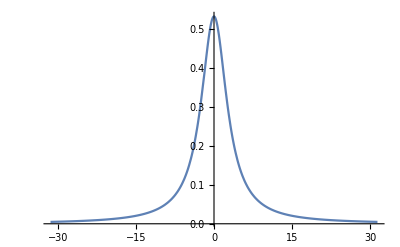

```mathematica
Plot[Abs[F11],{ω,-10 Pi,10Pi},PlotRange->All]
Plot[Abs[F12],{ω,-10 Pi,10Pi},PlotRange->All]
Plot[Abs[F21],{ω,-10 Pi,10Pi},PlotRange->All]
Plot[Abs[F22],{ω,-10 Pi,10Pi},PlotRange->All]
```

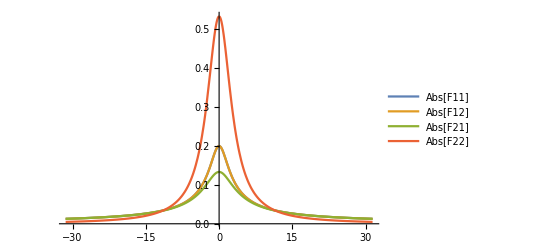

```mathematica
Plot[{Abs[F11],Abs[F12],Abs[F21],Abs[F22]},{ω,-10 Pi,10 Pi},PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
(*3*)
Clear["`*"];
f[t_]:=Exp[-a t^2];
F=FourierTransform[f[t],t,ω]
```

(ⅇ^(-ω^2/(4 a)))/(√2 √a)

```mathematica
Manipulate[Plot[Abs[(ⅇ^(-ω^2/(4 a)))/(√2 √a)],{ω,-10 Pi,10 Pi},PlotRange->All],{a,1.0,9.9,0.1}]
```

General::munfl: Exp[-246720.] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

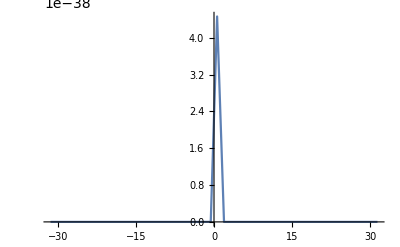

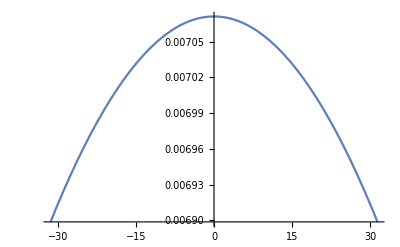

```mathematica
Plot[Abs[(ⅇ^(-ω^2/(4 0.001)))/(√2 √0.001)],{ω,-10 Pi,10 Pi},PlotRange->All]
Plot[Abs[(ⅇ^(-ω^2/(4 10000)))/(√2 √10000)],{ω,-10 Pi,10 Pi},PlotRange->All]
```

```mathematica
(*4*)
Clear["`*"];
F1[ω_]:=(ⅇ^(-ω^2/(4 1)))/(√2 √1) UnitBox[ω/1](*a==1*);
F2[ω_]:=(ⅇ^(-ω^2/(4 4)))/(√2 √4) UnitBox[ω/4](*a==4*);
F3[ω_]:=(ⅇ^(-ω^2/(4 9)))/(√2 √9) UnitBox[ω/9](*a==9*);
f1=InverseFourierTransform[F1[ω],ω,t]
f2=InverseFourierTransform[F2[ω],ω,t]
f3=InverseFourierTransform[F3[ω],ω,t]
```

1/2 ⅇ^(-t^2) (Erf[1/4-ⅈ t]+Erf[1/4+ⅈ t])

1/2 ⅇ^(-4 t^2) (Erf[1/2-2 ⅈ t]+Erf[1/2+2 ⅈ t])

1/2 ⅇ^(-9 t^2) (Erf[3/4-3 ⅈ t]+Erf[3/4+3 ⅈ t])

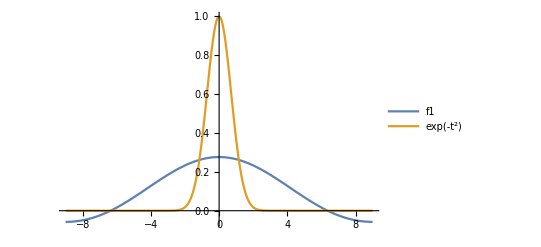

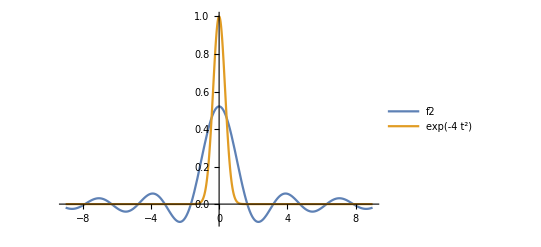

General::munfl: Exp[-728.94] 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

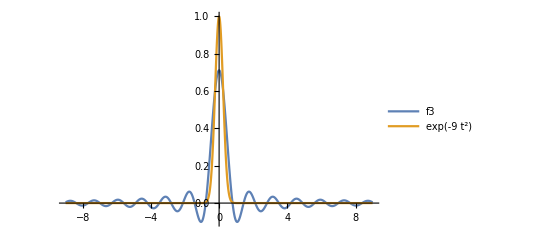

```mathematica
Plot[{f1,Exp[-t^2]},{t,-9,9},PlotRange->All,PlotLegends->"Expressions"]
Plot[{f2,Exp[-4 t^2]},{t,-9,9},PlotRange->All,PlotLegends->"Expressions"]
Plot[{f3,Exp[-9 t^2]},{t,-9,9},PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
(*3*)
```

```mathematica
Clear["`*"];
Convolve[UnitBox[x/3],UnitBox[x/4],x,y]
Convolve[Exp[-t^2-3 t],DiracDelta[t-3],t,y]
```

Piecewise[{{3, -1/2<y≤1/2}, {7/2-y, 1/2<y<7/2}, {7/2+y, -7/2<y≤-1/2}, {0, True}}]

ⅇ^(-((-3+y) y))

```mathematica
(*4*)
Clear["`*"];
f1[t_]:=Exp[-a t];
f2[t_]:=t^2+t+3+2 DiracDelta[t];
f3[t_]:=Sin[ω t+ψ];
LaplaceTransform[f1[t],t,s]
LaplaceTransform[f2[t],t,s]
LaplaceTransform[f3[t],t,s]
```

1/(a+s)

2+2/s^3+1/s^2+3/s

(ω Cos[ψ]+s Sin[ψ])/(s^2+ω^2)

```mathematica
(*5*)
Clear["`*"];
```

```mathematica
f1[t_]:=DiracDelta[t];
f2[t_]:=UnitStep[t];
f3[t_]:=Sin[t] UnitStep[t];
f4[t_]:=UnitStep[t]-UnitStep[t-2];
L1=LaplaceTransform[f1[t],t,s]
L2=LaplaceTransform[f2[t],t,s]
L3=LaplaceTransform[f3[t],t,s]
L4=LaplaceTransform[f4[t],t,s]
```

1

1/s

1/(1+s^2)

1/s-ⅇ^(-2 s)/s

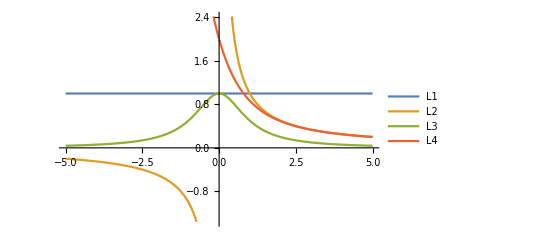

```mathematica
Plot[{L1,L2,L3,L4},{s,-5,5},PlotLegends->"Expressions"]
```

```mathematica
(*6*)
Clear["`*"];
F1[s_]:=(s^2-4)/(s^4+2 s^3-3 s^2+2 s+1);
Solve[s^2-4==0,s]
NSolve[s^4+2 s^3-3 s^2+2 s+1==0,s]
```

{{s→-2},{s→2}}

{{s→-3.13},{s→-0.319489},{s→0.724745-0.689017 ⅈ},{s→0.724745+0.689017 ⅈ}}

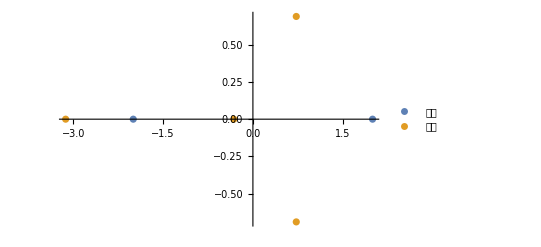

```mathematica
ListPlot[ReIm[{{2,-2},{-3.13,-0.319489,0.72475-0.689017I,0.724745+0.689017I}}],PlotLegends->{"零点","极点"}]
```

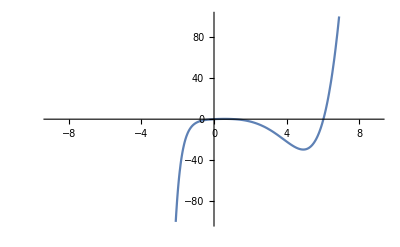

```mathematica
L1=InverseLaplaceTransform[F1[s],s,t];
Plot[L1,{t,-9,9},PlotRange->{{-9,9},{-100,100}}]
```

```mathematica
F2[s_]:=5 s(s^2+4 s+5)/(s^3+5 s^2+16s+30)
Solve[5 s(s^2+4 s+5)==0,s]
NSolve[s^3+5 s^2+16s+30==0,s]
```

{{s→-2-ⅈ},{s→-2+ⅈ},{s→0}}

{{s→-3.},{s→-1.-3. ⅈ},{s→-1.+3. ⅈ}}

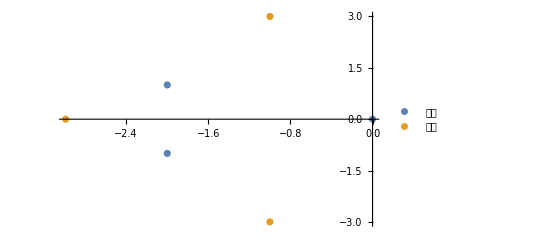

```mathematica
ListPlot[ReIm[{{-2-I,-2+I,0},{-2.99,-1.-3. ⅈ,-1.+3. ⅈ}}],PlotLegends->{"零点","极点"}]
```

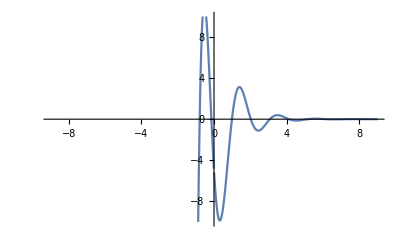

```mathematica
L2=InverseLaplaceTransform[F2[s],s,t];
Plot[L2,{t,-9,9},PlotRange->{{-9,9},{-10,10}}]
```

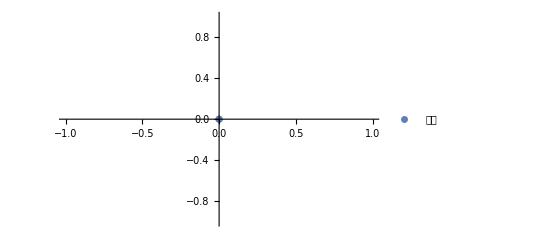

```mathematica
(*7*)
Clear["`*"];
H1[s_]:=1/s
ListPlot[ReIm[{0}],PlotLegends->{"极点"}]
```

1

1

x UnitStep[x]

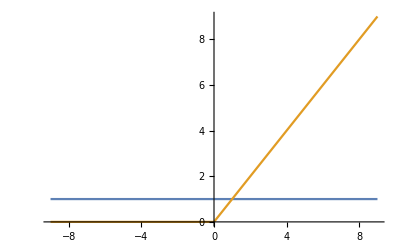

```mathematica
h1[t_]=InverseLaplaceTransform[H1[s],s,t]
c11=Convolve[h1[t],DiracDelta[t],t,x]
c12=Convolve[h1[t]UnitStep[t],UnitStep[t],t,x]
Plot[{c11,c12},{x,-9,9}]
```

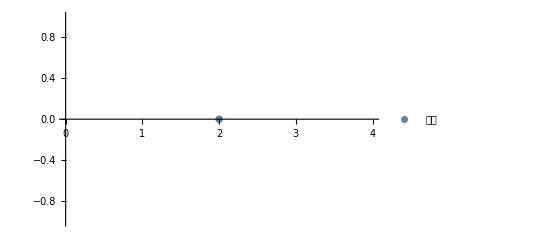

```mathematica
H2[s_]:=1/(s-2)
ListPlot[ReIm[{2}],PlotLegends->{"极点"}]
```

ⅇ^(2 t)

ⅇ^(2 x)

ⅇ^(2 x)/2

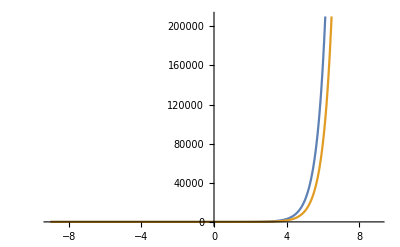

```mathematica
h2[t_]=InverseLaplaceTransform[H2[s],s,t]
c21=Convolve[h2[t],DiracDelta[t],t,x]
c22=Convolve[h2[t],UnitStep[t],t,x]
Plot[{c21,c22},{x,-9,9}]
```

{{s→-4 ⅈ},{s→4 ⅈ}}

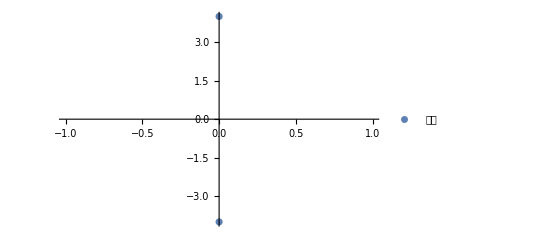

1/4 Sin[4 t]

1/4 Sin[4 x]

-1/16 Cos[4 x]

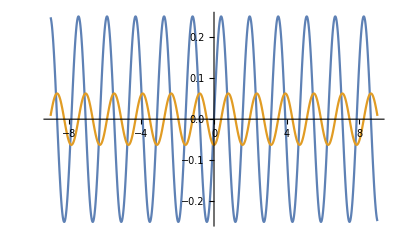

```mathematica
H3[s_]:=1/(s^2+16)
Solve[s^2+16==0,s]
ListPlot[ReIm[{-4I,4I}],PlotLegends->{"极点"}]
h3[t_]=InverseLaplaceTransform[H3[s],s,t]
c31=Convolve[h3[t],DiracDelta[t],t,x]
c32=Convolve[h3[t],UnitStep[t],t,x]
Plot[{c31,c32},{x,-9,9}]
```

```mathematica
H4[s_]:=1/(s^2+2 s+2)
Solve[s^2+2 s+2==0,s]
```

{{s→-1-ⅈ},{s→-1+ⅈ}}

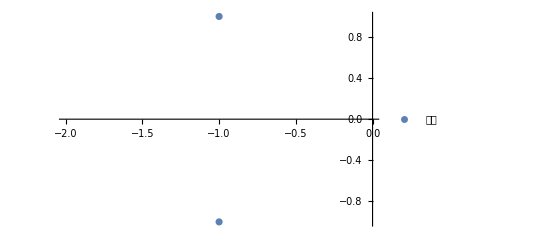

```mathematica
ListPlot[ReIm[{-1-I,-1+I}],PlotLegends->{"极点"}]
```

-1/2 ⅈ ⅇ^((-1-ⅈ) t) (-1+ⅇ^(2 ⅈ t))

ⅇ^-x Sin[x]

-1/2 ⅇ^Abs[x] (Cos[x]-Sin[Abs[x]])

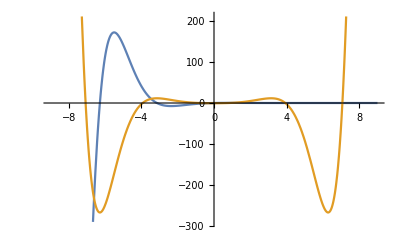

```mathematica
h4[t_]=InverseLaplaceTransform[H4[s],s,t]
c41=Convolve[h4[t],DiracDelta[t],t,x]
c42=Convolve[h4[t],UnitStep[t],t,x]
Plot[{c41,c42},{x,-9,9}]
```

```mathematica
H5[s_]:=1/((s-0.5)^2+16)
Solve[(s-0.5)^2+16==0,s]
```

{{s→0.5-4. ⅈ},{s→0.5+4. ⅈ}}

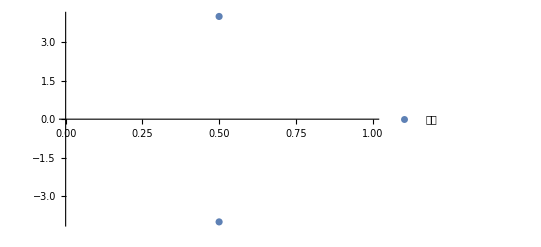

```mathematica
ListPlot[ReIm[{0.5-4. ⅈ,0.5+4. ⅈ}],PlotLegends->{"极点"}]
```

(0.+0.125 ⅈ) ⅇ^((0.5-4. ⅈ) t)-(0.+0.125 ⅈ) ⅇ^((0.5+4. ⅈ) t)

(0.+0.125 ⅈ) ⅇ^((0.5-4. ⅈ) x)-(0.+0.125 ⅈ) ⅇ^((0.5+4. ⅈ) x)

(0.0615385-(0.0307692-0.00384615 ⅈ) ⅇ^((0.5-4. ⅈ) x)-(0.0307692+0.00384615 ⅈ) ⅇ^((0.5+4. ⅈ) x)) UnitStep[x]

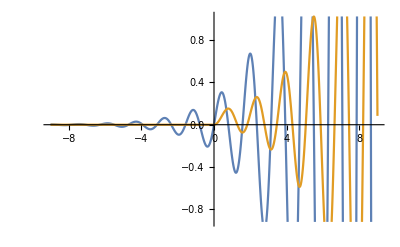

```mathematica
h5[t_]=InverseLaplaceTransform[H5[s],s,t]
c51=Convolve[h5[t],DiracDelta[t],t,x]
c52=Convolve[h5[t] UnitStep[t],UnitStep[t],t,x]
Plot[{c51,c52},{x,-9,9}]
```

```mathematica
H6[s_]:=1/((s+0.5)^2+16)
Solve[(s+0.5)^2+16==0,s]
```

{{s→-0.5-4. ⅈ},{s→-0.5+4. ⅈ}}

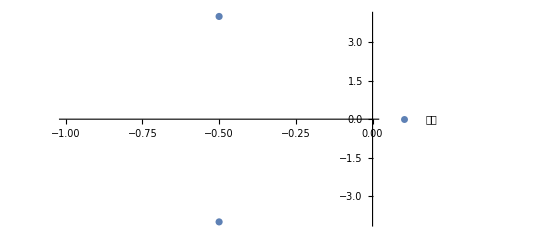

```mathematica
ListPlot[ReIm[{-0.5-4. ⅈ,-0.5+4. ⅈ}],PlotLegends->{"极点"}]
```

ⅇ^((-0.5-4. ⅈ) t) ((0.+0.125 ⅈ)-(0.+0.125 ⅈ) ⅇ^((0.+8. ⅈ) t))

(0.+0.125 ⅈ) ⅇ^((-0.5-4. ⅈ) x)-(0.+0.125 ⅈ) ⅇ^((-0.5+4. ⅈ) x)

(-0.0307692+0.00384615 ⅈ) ⅇ^((-0.5+4. ⅈ) x)-(0.0307692+0.00384615 ⅈ) ⅇ^((-0.5-4. ⅈ) x)

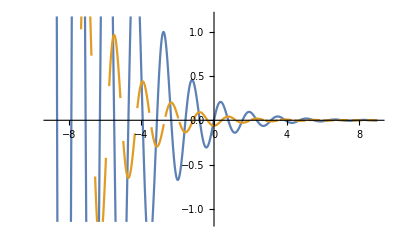

```mathematica
h6[t_]=InverseLaplaceTransform[H6[s],s,t]
c61=Convolve[h6[t],DiracDelta[t],t,x]
c62=Convolve[h6[t],UnitStep[t],t,x]
Plot[{c61,c62},{x,-9,9}]
```

```mathematica
Clear["`*"]
H[s_]:=1/(s^3+2 s^2+2 s+1)
Solve[s^3+2 s^2+2 s+1==0,s]
```

{{s→-1},{s→-(-1)^(1/3)},{s→(-1)^(2/3)}}

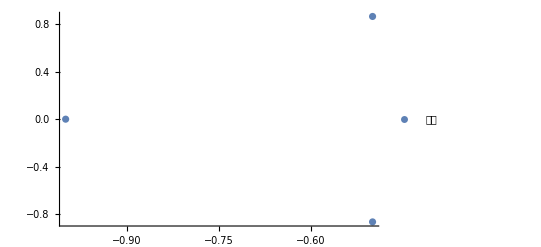

```mathematica
ListPlot[ReIm[{-1,-(-1)^(1/3),(-1)^(2/3)}],PlotLegends->{"极点"}]
```

ⅇ^-t-(ⅇ^(-t/2) (√3 Cos[(√3 t)/2]-Sin[(√3 t)/2]))/(√3)

ⅇ^-x-(ⅇ^(-x/2) (√3 Cos[(√3 x)/2]-Sin[(√3 x)/2]))/(√3)

(1-ⅇ^-x-(2 ⅇ^(-x/2) Sin[(√3 x)/2])/(√3)) UnitStep[x]

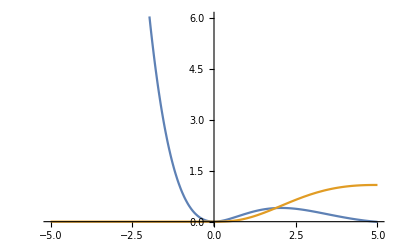

```mathematica
H7[s_]:=1/(s^3+2 s^2+2 s+1)
h7[t_]=InverseLaplaceTransform[H7[s],s,t]
c71=Convolve[h[t],DiracDelta[t],t,x]
c72=Convolve[h[t]UnitStep[t],UnitStep[t],t,x]
Plot[{c71,c72},{x,-5,5}]
```

```mathematica
H8[s_]:=(s^2-2 s+0.8)/(s^3+2 s^2+2 s+1)
Solve[s^2-2 s+0.8==0,s]
Solve[s^3+2 s^2+2 s+1==0,s]
```

{{s→0.552786},{s→1.44721}}

{{s→-1},{s→-(-1)^(1/3)},{s→(-1)^(2/3)}}

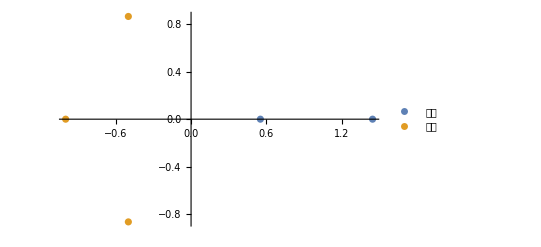

```mathematica
ListPlot[ReIm[{{0.552786,1.44721},{-1,-(-1)^(1/3),(-1)^(2/3)}}],PlotLegends->{"零点","极点"}]
```

3.8 ⅇ^(-1. t)-(1.4+0.92376 ⅈ) ⅇ^((-0.5-0.866025 ⅈ) t)-(1.4-0.92376 ⅈ) ⅇ^((-0.5+0.866025 ⅈ) t)

3.8 ⅇ^(-1. x)-(1.4+0.92376 ⅈ) ⅇ^((-0.5-0.866025 ⅈ) x)-(1.4-0.92376 ⅈ) ⅇ^((-0.5+0.866025 ⅈ) x)

-3.8 ⅇ^-x+(1.5+0.750555 ⅈ) ⅇ^((-0.5+0.866025 ⅈ) x)+(1.5-0.750555 ⅈ) ⅇ^((-0.5-0.866025 ⅈ) x)

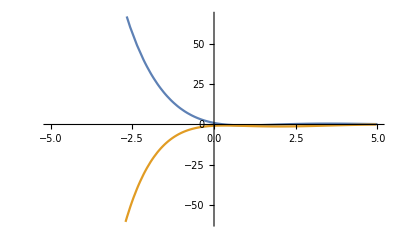

```mathematica
h8[t_]=InverseLaplaceTransform[H8[s],s,t]
c81=Convolve[h8[t],DiracDelta[t],t,x]
c82=Convolve[h8[t],UnitStep[t],t,x]
Plot[{c81,c82},{x,-5,5}]
```

```mathematica
(*8*)
Clear["`*"];
DSolve[{6 D[y[t],{t,6}]+10 D[y[t],{t,5}]+48 D[y[t],{t,4}]+148D[y[t],{t,3}]+306 D[y[t],{t,2}]+401D[y[t],t]+262y[t]==262DiracDelta[t],y'''''[0]==0,y''''[0]==0,y'''[0]==0,y''[0]==0,y'[0]==0,y[0]==0},y[t],t]
```

```mathematica
DSolve[{6 D[y[t],{t,6}]+10 D[y[t],{t,5}]+48 D[y[t],{t,4}]+148D[y[t],{t,3}]+306 D[y[t],{t,2}]+401D[y[t],t]+262y[t]==262UnitStep[t],y'''''[0]==0,y''''[0]==0,y'''[0]==0,y''[0]==0,y'[0]==0,y[0]==0},y[t],t]
```